```mathematica
w=Compile[{β},
ω/.Solve[{1==-ArcTan[β/Abs[ω]]/(√(β^2+ω^2)),ω≥0},{ω},Reals][[1]]]
data = Table[{β,w[β]},{β,-π/2,0,0.01}]
data2 = Table[{β,w[β]},{β,-1.5,0,0.02}]
ifun = Interpolation[data];
Plot[{ifun[β]}, {β,-π/2,0}, PlotRange->{{-π/2,0}},Axes->{True,True}, Epilog->Map[Point,data]]
```

CompiledFunction[{β},ω/.Solve[{1==-ArcTan[β/Abs[ω]]/(√(β^2+ω^2)),ω≥0},{ω},Reals]⟦1⟧,-CompiledCode-]

{{-1.5708,9.62076×10^-17},{-1.5608,0.0154885},{-1.5508,0.0305532},{-1.5408,0.0452149},{-1.5308,0.0594928},{-1.5208,0.0734042},{-1.5108,0.0869653},{-1.5008,0.100191},{-1.4908,0.113094},{-1.4808,0.125688},{-1.4708,0.137983},{-1.4608,0.149992},{-1.4508,0.161724},{-1.4408,0.173187},{-1.4308,0.184392},{-1.4208,0.195346},{-1.4108,0.206057},{-1.4008,0.216531},{-1.3908,0.226777},{-1.3808,0.236799},{-1.3708,0.246604},{-1.3608,0.256198},{-1.3508,0.265587},{-1.3408,0.274774},{-1.3308,0.283764},{-1.3208,0.292564},{-1.3108,0.301175},{-1.3008,0.309603},{-1.2908,0.317852},{-1.2808,0.325924},{-1.2708,0.333824},{-1.2608,0.341555},{-1.2508,0.34912},{-1.2408,0.356522},{-1.2308,0.363763},{-1.2208,0.370847},{-1.2108,0.377775},{-1.2008,0.384551},{-1.1908,0.391177},{-1.1808,0.397655},{-1.1708,0.403987},{-1.1608,0.410175},{-1.1508,0.416221},{-1.1408,0.422127},{-1.1308,0.427895},{-1.1208,0.433526},{-1.1108,0.439022},{-1.1008,0.444384},{-1.0908,0.449615},{-1.0808,0.454714},{-1.0708,0.459684},{-1.0608,0.464526},{-1.0508,0.469241},{-1.0408,0.47383},{-1.0308,0.478295},{-1.0208,0.482635},{-1.0108,0.486853},{-1.0008,0.490949},{-0.990796,0.494924},{-0.980796,0.498778},{-0.970796,0.502513},{-0.960796,0.506129},{-0.950796,0.509627},{-0.940796,0.513008},{-0.930796,0.516271},{-0.920796,0.519418},{-0.910796,0.522449},{-0.900796,0.525364},{-0.890796,0.528165},{-0.880796,0.53085},{-0.870796,0.533421},{-0.860796,0.535878},{-0.850796,0.53822},{-0.840796,0.540449},{-0.830796,0.542564},{-0.820796,0.544566},{-0.810796,0.546454},{-0.800796,0.548228},{-0.790796,0.549889},{-0.780796,0.551436},{-0.770796,0.552869},{-0.760796,0.554189},{-0.750796,0.555394},{-0.740796,0.556485},{-0.730796,0.557462},{-0.720796,0.558323},{-0.710796,0.559069},{-0.700796,0.559699},{-0.690796,0.560213},{-0.680796,0.560611},{-0.670796,0.56089},{-0.660796,0.561052},{-0.650796,0.561095},{-0.640796,0.561019},{-0.630796,0.560822},{-0.620796,0.560504},{-0.610796,0.560064},{-0.600796,0.559501},{-0.590796,0.558814},{-0.580796,0.558001},{-0.570796,0.557062},{-0.560796,0.555995},{-0.550796,0.554798},{-0.540796,0.553471},{-0.530796,0.552012},{-0.520796,0.550418},{-0.510796,0.548689},{-0.500796,0.546822},{-0.490796,0.544816},{-0.480796,0.542667},{-0.470796,0.540375},{-0.460796,0.537936},{-0.450796,0.535348},{-0.440796,0.532608},{-0.430796,0.529714},{-0.420796,0.526662},{-0.410796,0.523449},{-0.400796,0.520071},{-0.390796,0.516525},{-0.380796,0.512807},{-0.370796,0.508912},{-0.360796,0.504836},{-0.350796,0.500574},{-0.340796,0.496121},{-0.330796,0.49147},{-0.320796,0.486616},{-0.310796,0.481553},{-0.300796,0.476272},{-0.290796,0.470766},{-0.280796,0.465028},{-0.270796,0.459047},{-0.260796,0.452813},{-0.250796,0.446315},{-0.240796,0.439542},{-0.230796,0.43248},{-0.220796,0.425113},{-0.210796,0.417426},{-0.200796,0.4094},{-0.190796,0.401013},{-0.180796,0.392243},{-0.170796,0.383063},{-0.160796,0.373441},{-0.150796,0.363342},{-0.140796,0.352725},{-0.130796,0.341542},{-0.120796,0.329732},{-0.110796,0.317227},{-0.100796,0.303941},{-0.0907963,0.289763},{-0.0807963,0.274558},{-0.0707963,0.258141},{-0.0607963,0.240264},{-0.0507963,0.220573},{-0.0407963,0.198526},{-0.0307963,0.173226},{-0.0207963,0.142956},{-0.0107963,0.103437},{-0.000796327,0.0282099}}

```mathematica
w[-1.5]
```

0.10123

```mathematica
w[-0.1]
```

0.302846

```mathematica
w[-1.4]
```

0.217355

```mathematica
w[-1.49]
```

0.114108

{{-1.5708,0},{-1.5,0},{-1.48,0.126678},{-1.46,0.150936},{-1.44,0.174089},{-1.42,0.196208},{-1.4,0.217355},{-1.38,0.237588},{-1.36,0.256954},{-1.34,0.275497},{-1.32,0.293256},{-1.3,0.310267},{-1.28,0.32656},{-1.26,0.342164},{-1.24,0.357104},{-1.22,0.371404},{-1.2,0.385084},{-1.18,0.398165},{-1.16,0.410662},{-1.14,0.422592},{-1.12,0.433969},{-1.1,0.444806},{-1.08,0.455115},{-1.06,0.464906},{-1.04,0.474191},{-1.02,0.482976},{-1.,0.49127},{-0.98,0.49908},{-0.96,0.506412},{-0.94,0.513272},{-0.92,0.519664},{-0.9,0.525592},{-0.88,0.531059},{-0.86,0.536068},{-0.84,0.540622},{-0.82,0.54472},{-0.8,0.548364},{-0.78,0.551554},{-0.76,0.554289},{-0.74,0.556567},{-0.72,0.558387},{-0.7,0.559745},{-0.68,0.560637},{-0.66,0.56106},{-0.64,0.561007},{-0.62,0.560474},{-0.6,0.559451},{-0.58,0.557931},{-0.56,0.555904},{-0.54,0.55336},{-0.52,0.550285},{-0.5,0.546667},{-0.48,0.54249},{-0.46,0.537735},{-0.44,0.532384},{-0.42,0.526412},{-0.4,0.519795},{-0.38,0.512503},{-0.36,0.504504},{-0.34,0.495757},{-0.32,0.486221},{-0.3,0.475842},{-0.28,0.464561},{-0.26,0.452305},{-0.24,0.438991},{-0.22,0.424513},{-0.2,0.408746},{-0.18,0.391528},{-0.16,0.372655},{-0.14,0.351856},{-0.12,0.328763},{-0.1,0.302846},{-0.08,0.273298},{-0.06,0.238769},{-0.04,0.196646},{-0.02,0.140239},{-0.0107963,0.103437},{0,0}}

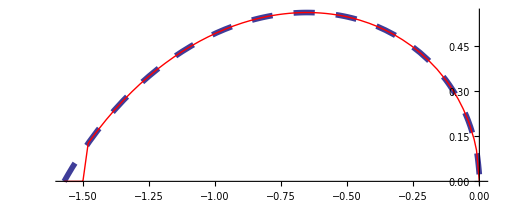

```mathematica
data3={{-1.5707963267948966,0},{-1.5,0},{-1.48,0.12667759913660323},{-1.46,0.15093632021534908},{-1.44,0.1740889729238732},{-1.42,0.19620763796823112},{-1.4,0.21735536362425095},{-1.38,0.2375876337394377},{-1.36,0.25695353879691024},{-1.34,0.27549672019952404},{-1.32,0.2932561391134172},{-1.3,0.310266707986698},{-1.28,0.3265598134161952},{-1.26,0.3421637521922693},{-1.24,0.35710409732547094},{-1.22,0.37140400712087956},{-1.2,0.38508448755394015},{-1.18,0.3981646160634735},{-1.16,0.41066173323547256},{-1.14,0.42259160757835834},{-1.1199999999999999,0.43396857759478313},{-1.1,0.44480567456980646},{-1.08,0.455114728870821},{-1.06,0.4649064620540659},{-1.04,0.4741905666681674},{-1.02,0.4829757753157585},{-1.,0.4912699202637119},{-0.98,0.49907998466831743},{-0.96,0.5064121462941016},{-0.94,0.5132718144461742},{-0.92,0.5196636606998366},{-0.9,0.5255916438926883},{-0.88,0.5310590297394808},{-0.86,0.5360684053350051},{-0.84,0.5406216887223191},{-0.82,0.5447201336198877},{-0.7999999999999999,0.5483643293191642},{-0.78,0.5515541956812563},{-0.76,0.5542889730750009},{-0.74,0.5565672070062148},{-0.72,0.5583867270859203},{-0.7,0.5597446198702903},{-0.6799999999999999,0.5606371949724566},{-0.66,0.5610599436907245},{-0.64,0.5610074892122587},{-0.62,0.5604735272271891},{-0.6,0.559450755514019},{-0.58,0.55793079071838},{-0.5599999999999999,0.5559040701239885},{-0.54,0.5533597356809338},{-0.52,0.5502854968767855},{-0.5,0.5466674681621349},{-0.48,0.542489975507317},{-0.45999999999999996,0.5377353251778646},{-0.44,0.5323835258405473},{-0.42,0.5264119524599131},{-0.39999999999999997,0.5197949368406612},{-0.38,0.5125032647047931},{-0.36,0.5045035522481277},{-0.33999999999999997,0.4957574652526814},{-0.31999999999999995,0.48622072955755274},{-0.3,0.4758418606350008},{-0.27999999999999997,0.46456050827183587},{-0.25999999999999995,0.4523052633052248},{-0.23999999999999996,0.43899069545122177},{-0.21999999999999997,0.42451326356033675},{-0.19999999999999998,0.4087455226094965},{-0.17999999999999997,0.39152766709025716},{-0.15999999999999998,0.372654734099997},{-0.13999999999999996,0.35185637380207535},{-0.11999999999999997,0.32876308688938133},{-0.09999999999999998,0.30284582760378065},{-0.07999999999999997,0.2732975261142474},{-0.05999999999999997,0.2387685440573553},{-0.039999999999999966,0.19664620906340496},{-0.01999999999999997,0.1402392494605471},{-0.010796326794896526,0.10343719133295229},{0,0}}
ifun3 = Interpolation[data3,InterpolationOrder->1];
Plot[{ifun[β], ifun3[β]}, {β,-π/2,0}, PlotRange->{{-π/2,0}},PlotStyle ->{Directive[Thickness[0.008],Dashing[0.03]], Directive[Red]}, Axes->{True,True},AspectRatio->Automatic,AxesStyle->Directive[FontSize->16,FontFamily->"TimesNewRoman"]]
```